```mathematica
$Assumptions = $Assumptions && {Δ, Θ, ω, V,Λ} ∈ PositiveReals&& {d}∈ PositiveIntegers && {m, q, Σ} ∈ Reals;
```

### Elements dependent on the loss function

#### Case of L2 Loss

```mathematica
foutL2 = FullSimplify[
(y-ω)/(1+V)
]
```

(y-ω)/(1+V)

```mathematica
DfoutL2 = FullSimplify[
D[foutL2, ω]
]
```

-1/(1+V)

```mathematica
ffoutL2 = FullSimplify[
foutL2 /. {y -> y, ω -> √q ξ, V -> Σ}
]
```

(y-√q ξ)/(1+Σ)

```mathematica
DDfoutL2 = FullSimplify[
DfoutL2 /. {y -> y, ω -> √q ξ, V -> Σ}
]
```

-1/(1+Σ)

#### Case of L1 Loss

```mathematica
foutL1 = FullSimplify[

]
```

FullSimplify::argt: FullSimplify called with 0 arguments; 1 or 2 arguments are expected.

FullSimplify[]

```mathematica
DfoutL1 = FullSimplify[

]
```

FullSimplify::argt: FullSimplify called with 0 arguments; 1 or 2 arguments are expected.

FullSimplify[]

#### Case of Huber Loss

```mathematica
foutHuber = FullSimplify[

]
```

FullSimplify::argt: FullSimplify called with 0 arguments; 1 or 2 arguments are expected.

FullSimplify[]

```mathematica
DfoutHuber = FullSimplify[

]
```

FullSimplify::argt: FullSimplify called with 0 arguments; 1 or 2 arguments are expected.

FullSimplify[]

## Simple case with ϵ = 0

Now we want to calculate the Zout^\star

```mathematica
ZoutBayes = FullSimplify[
Integrate[1/(√(2π))Exp[-z^2/2] 1/(√(2π Δ))Exp[-1/(2Δ)(y-√V z-ω)^2],
{z,-∞, ∞}
]
]
```

(ⅇ^(-(y-ω)^2/(2 (V+Δ))))/(√(2 π) √(V+Δ))

```mathematica
foutBayes = FullSimplify[
D[Log[(ⅇ^(-(y-ω)^2/(2 (V+Δ))))/(√(2 π) √(V+Δ))], ω]
]
```

(y-ω)/(V+Δ)

```mathematica
DfoutBayes = FullSimplify[
D[(y-ω)/(V+Δ),ω]
]
```

-1/(V+Δ)

```mathematica
ZwBayes = FullSimplify[
Integrate[
1/(√(2π))Exp[-z^2/2]Exp[-1/2 Λ z^2+γ z],
{z,-∞, ∞}
]
]
```

(ⅇ^(γ^2/(2+2 Λ)))/(√(1+Λ))

```mathematica
fwBayes = FullSimplify[
D[Log[(ⅇ^(γ^2/(2+2 Λ)))/(√(1+Λ))], γ]
]
```

γ/(1+Λ)

```mathematica
DfwBayes = FullSimplify[
D[γ/(1+Λ), γ]
]
```

1/(1+Λ)

Now let’s integrate to obtain the fixed points equations. First we need to consider the above quantities evaluated in different points.

```mathematica
η = m^2/q;
```

```mathematica
ZZoutBayes = FullSimplify[
ReplaceAll[
ZoutBayes ,
{y-> y, ω-> Sqrt[η]ξ, V -> (1-η)}
]
]
```

(ⅇ^(-(q (y-√(1/q) ξ Abs[m])^2)/(2 (-m^2+q+q Δ))))/(√(2 π) √(1-m^2/q+Δ))

```mathematica
ffoutBayes = FullSimplify[
ReplaceAll[
foutBayes,
{y-> y, ω-> Sqrt[q]ξ, V ->Σ}
]
]
```

(y-√q ξ)/(Δ+Σ)

```mathematica
DDfoutBayes = FullSimplify[
ReplaceAll[
DfoutBayes,
{y-> y, ω-> Sqrt[q]ξ, V ->Σ}
]
]
```

-1/(Δ+Σ)

### Small research of probability distribution

What is the PDF of  the product of two normally distributed RVs?

```mathematica
MGF = FullSimplify[
Integrate[
1/Sqrt[2π] Exp[-1/2 x^2] 1/Sqrt[2π] Exp[-1/2 y^2]Exp[ⅈ x y t],
{x,-∞, ∞},{y,-∞, ∞}
],
Assumptions->{t ∈Reals}
]
```

Integrate::fas: Warning: one or more assumptions evaluated to False.

1/(√(1+t^2))

The pdf of the scalar product of X and θ is the following

```mathematica
PDFy = (Abs[y]^((d-1)/2)BesselK[(d-1)/2,Abs[y]])/(2^((d-1)/2)Sqrt[π]Gamma[d/2])
```

(2^((1-d)/2) Abs[y]^(1/2 (-1+d)) BesselK[1/2 (-1+d),Abs[y]])/(√π Gamma[d/2])

```mathematica
Integrate[
1/Sqrt[2π Δ] Exp[-1/2 z^2/Δ](2^((1-d)/2) Abs[y]^(1/2 (-1+d)) BesselK[1/2 (-1+d),Abs[y]])/(√π Gamma[d/2])DiracDelta[y+z-x],
 {z,-∞,∞},{y,-∞,∞},
Assumptions->{x ∈ Reals, d ∈PositiveIntegers}
]
```

Integrate[(2^(-d/2) ⅇ^(-z^2/(2 Δ)) Abs[x-z]^(1/2 (-1+d)) BesselK[1/2 (-1+d),Abs[x-z]])/(π √Δ Gamma[d/2]),{z,-∞,∞},Assumptions→{x∈ℝ,d∈ℤ&&d>0}]

```mathematica
InverseFourierTransform[
1/((1+t^2)^(d/2))Exp[-1/2 Δ t^2],t, x,
FourierParameters->{1,1},
Assumptions-> {d ∈PositiveIntegers}
]
```

InverseFourierTransform[ⅇ^(-(t^2 Δ)/2) (1+t^2)^(-d/2),t,x,FourierParameters→{1,1},Assumptions→{d∈ℤ&&d>0}]

```mathematica
Integrate[
1/((1+t^2)^(d/2))Exp[-1/2 Δ t^2]Exp[-ⅈ t x],
{t, -∞, ∞},
Assumptions->{x ∈ Reals}
]
```

Integrate[ⅇ^(-ⅈ t x-(t^2 Δ)/2) (1+t^2)^(-d/2),{t,-∞,∞},Assumptions→{x∈ℝ}]

```mathematica
Integrate[
t^(2n)Exp[-1/2 t^2]Exp[-ⅈ t x],
{t, -∞, ∞},
Assumptions->{n ∈ PositiveIntegers, x ∈ Reals}
]
```

2^n (((1+(-1)^(2 n)) Gamma[1/2+n] Hypergeometric1F1[1/2+n,1/2,-x^2/2])/(√2)+ⅈ (-1+(-1)^(2 n)) x Gamma[1+n] Hypergeometric1F1[1+n,3/2,-x^2/2])

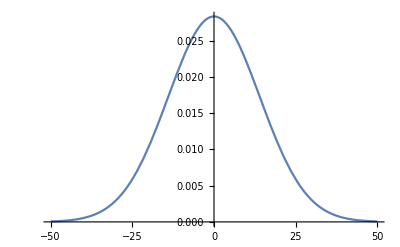

```mathematica
Plot[PDFy/.{d-> 200},{y,-50,50}]
```

### Continue of the original calculation

Now we consider the actual fixed point equations, but before we substitute the arguments

```mathematica
mhat = α FullSimplify[
Integrate[
1/(√(2π))Exp[-ξ^2/2] ZZoutBayes ffoutBayes ffoutL2,
{y, -∞, ∞},{ξ, -∞, ∞}
]
]
```

ConditionalExpression[(α (-2 √(1/q) √(q^3) Abs[m]+(1+q+Δ) Abs[q]))/((1+Σ) (Δ+Σ) Abs[q]), q+q Δ≥m^2||q≤0]

```mathematica
mhat = α Integrate[
1/(√(2π))Exp[-ξ^2/2] ZZoutBayes ffoutBayes ffoutL2,
{ξ, -∞, ∞}, {y, -∞, ∞}
]
```

ConditionalExpression[(α (1+q+Δ-2 √(1/q) √q Abs[m]))/((1+Σ) (Δ+Σ)), q+q Δ≥m^2||q≤0]

```mathematica
qhat = α FullSimplify[
Integrate[
1/(√(2π))Exp[-ξ^2/2] ZZoutBayes (ffoutL2)^2,
{y, -∞, ∞},{ξ, -∞, ∞}
]
]
```

ConditionalExpression[(α (1+q+Δ-(2 m (1/q)^(5/2) √(q^5))/Sign[m]))/(1+Σ)^2, q+q Δ≥m^2||q≤0]

```mathematica
qhat = α Integrate[
1/(√(2π))Exp[-ξ^2/2] ZZoutBayes (ffoutL2)^2,
{ξ, -∞, ∞}, {y, -∞, ∞}
]
```

ConditionalExpression[(α (1+q+Δ-2 √(1/q) √q Abs[m]))/(1+Σ)^2, q+q Δ≥m^2||q≤0]

```mathematica
Σhat = -α FullSimplify[
Integrate[
1/(√(2π))Exp[-ξ^2/2]ZZoutBayes DDfoutL2,
{y, -∞, ∞},{ξ, -∞, ∞}
]
]
```

ConditionalExpression[α/(1+Σ), q+q Δ≥m^2||q≤0]

```mathematica
Σhat = -α Integrate[
1/(√(2π))Exp[-ξ^2/2]ZZoutBayes DDfoutL2,
{ξ, -∞, ∞}, {y, -∞, ∞}
]
```

ConditionalExpression[α/(1+Σ), q+q Δ≥m^2||q≤0]

## Case of ϵ != 0

```mathematica
Assuming[
{Δ ∈ PositiveReals,Θ ∈ PositiveReals,ω ∈ PositiveReals, V ∈ PositiveReals},
FullSimplify[Integrate[1/(√(2π))((1-ϵ)/(√(2π Δ))Exp[-z^2/2] Exp[-1/(2Δ)(y-√V z-ω)^2]+ϵ/(√(2π Θ))Exp[-z^2/2] Exp[-1/(2Θ)(y-√V z-ω)^2]),{z,-∞,∞}]
]
]
```

(ⅇ^(-((2 V+Δ+Θ) (y-ω)^2)/(2 (V+Δ) (V+Θ))) (ⅇ^((y-ω)^2/(2 (V+Δ))) √(V+Δ) ϵ-ⅇ^((y-ω)^2/(2 (V+Θ))) (-1+ϵ) √(V+Θ)))/(√(2 π) √((V+Δ) (V+Θ)))

```mathematica
Assuming[
{Δ ∈ PositiveReals,Θ ∈ PositiveReals,ω ∈ PositiveReals, V ∈ PositiveReals},
FullSimplify[Integrate[1/(√(2π))((1-ϵ)/(√(2π Δ))Exp[-z^2/2] Exp[-1/(2Δ)(y-√V z-ω)^2]),{z,-∞,∞}]
]
]
```

-(ⅇ^(-(y-ω)^2/(2 (V+Δ))) (-1+ϵ))/(√(2 π) √(V+Δ))

```mathematica
Assuming[
{Δ ∈ PositiveReals,Θ ∈ PositiveReals,ω ∈ PositiveReals, V ∈ PositiveReals},
FullSimplify[Integrate[1/(√(2π))(ϵ/(√(2π Θ))Exp[-z^2/2] Exp[-1/(2Θ)(y-√V z-ω)^2]),{z,-∞,∞}]
]
]
```

(ⅇ^(-(y-ω)^2/(2 (V+Θ))) ϵ)/(√(2 π) √(V+Θ))

```mathematica
Assuming[
{Δ ∈ PositiveReals,Θ ∈ PositiveReals, ω ∈ PositiveReals, V ∈ PositiveReals},
FullSimplify[
D[
FullSimplify[Log[(1-ϵ)(ⅇ^(-(y-ω)^2/(2 (V+Δ))))/(√(2 π) √(V+Δ))+(ⅇ^(-(y-ω)^2/(2 (V+Θ))) ϵ)/(√(2 π) √(V+Θ))]],
ω]
]
]
```

((-ⅇ^((y-ω)^2/(2 (V+Δ))) (V+Δ)^(3/2) ϵ+ⅇ^((y-ω)^2/(2 (V+Θ))) (-1+ϵ) (V+Θ)^(3/2)) (y-ω))/((V+Δ) (V+Θ) (-ⅇ^((y-ω)^2/(2 (V+Δ))) √(V+Δ) ϵ+ⅇ^((y-ω)^2/(2 (V+Θ))) (-1+ϵ) √(V+Θ)))

```mathematica
Assuming[
{Δ ∈ PositiveReals,Θ ∈ PositiveReals, ω ∈ PositiveReals, V ∈ PositiveReals},
FullSimplify[
D[
((-ⅇ^((y-ω)^2/(2 (V+Δ))) (V+Δ)^(3/2) ϵ+ⅇ^((y-ω)^2/(2 (V+Θ))) (-1+ϵ) (V+Θ)^(3/2)) (y-ω))/((V+Δ) (V+Θ) (-ⅇ^((y-ω)^2/(2 (V+Δ))) √(V+Δ) ϵ+ⅇ^((y-ω)^2/(2 (V+Θ))) (-1+ϵ) √(V+Θ))),
ω]
]
]
```

(-1+(ⅇ^((y-ω)^2/(2 (V+Δ))) ϵ (Δ-Θ) ((ⅇ^((y-ω)^2/(2 (V+Δ))) ϵ (-Δ+Θ) (y-ω)^2)/((ⅇ^((y-ω)^2/(2 (V+Δ))) √(V+Δ) ϵ-ⅇ^((y-ω)^2/(2 (V+Θ))) (-1+ϵ) √(V+Θ))^2)+(V^2-y^2 Δ+y^2 Θ+Δ Θ+V (Δ+Θ)+2 y (Δ-Θ) ω+(-Δ+Θ) ω^2)/(-ⅇ^((y-ω)^2/(2 (V+Δ))) (V+Δ) ϵ+ⅇ^((y-ω)^2/(2 (V+Θ))) (-1+ϵ) √((V+Δ) (V+Θ)))))/(V+Θ)^2)/(V+Δ)

### Test to obtain the same results as in the paper 2006.06560

```mathematica
FullSimplify[
(1/Sqrt[2 π Δ] Exp[-1/2(y-1)^2/Δ]-1/Sqrt[2 π Δ] Exp[-1/2(y+1)^2/Δ])/(1/(√(2π Δ))Exp[-(y-1)^2/(2 Δ)] 1/2(1+Erf[ω/Sqrt[2 V]]) +1/(√(2π Δ))Exp[-(y+1)^2/(2 Δ)] 1/2(1-Erf[ω/Sqrt[2 V]]) )1/Sqrt[2 π V] Exp[-1/2 ω^2/V]
]
```

(ⅇ^(-ω^2/(2 V)) (-1+ⅇ^((2 y)/Δ)) √(2/π))/(√V (1+ⅇ^((2 y)/Δ)+(-1+ⅇ^((2 y)/Δ)) Erf[ω/(√2 √V)]))

```mathematica
(ⅇ^(-ω^2/(2 V)) (-1+ⅇ^((2 y)/Δ)) √(2/π))/(√V (1+ⅇ^((2 y)/Δ)+(-1+ⅇ^((2 y)/Δ)) Erf[ω/(√2 √V)]))/.{y-> y, ω-> Sqrt[η]ξ, V -> (1-η)}
```

(ⅇ^(-(m^2 ξ^2)/(2 (1-m^2/q) q)) (-1+ⅇ^((2 y)/Δ)) √(2/π))/(√(1-m^2/q) (1+ⅇ^((2 y)/Δ)+(-1+ⅇ^((2 y)/Δ)) Erf[(√(m^2/q) ξ)/(√2 √(1-m^2/q))]))

```mathematica
(ⅇ^(-ω^2/(2 V)) (1+ⅇ^((2 y)/Δ)) √(2/π))/(√V (1+ⅇ^((2 y)/Δ)+(-1+ⅇ^((2 y)/Δ)) Erf[ω/(√2 √V)]))/.{y-> y, ω-> Sqrt[η]ξ, V -> (1-η)}
```

(ⅇ^(-(m^2 ξ^2)/(2 (1-m^2/q) q)) (1+ⅇ^((2 y)/Δ)) √(2/π))/(√(1-m^2/q) (1+ⅇ^((2 y)/Δ)+(-1+ⅇ^((2 y)/Δ)) Erf[(√(m^2/q) ξ)/(√2 √(1-m^2/q))]))

```mathematica
(1/(√(2π Δ))Exp[-(y-1)^2/(2 Δ)] 1/2(1+Erf[ω/Sqrt[2 V]]) +1/(√(2π Δ))Exp[-(y+1)^2/(2 Δ)] 1/2(1-Erf[ω/Sqrt[2 V]]) ) /.{y-> y, ω-> Sqrt[η]ξ, V -> (1-η)}
```

(ⅇ^(-(1+y)^2/(2 Δ)) (1-Erf[(√η ξ)/(√2 √(1-η))]))/(2 √(2 π) √Δ)+(ⅇ^(-(-1+y)^2/(2 Δ)) (1+Erf[(√η ξ)/(√2 √(1-η))]))/(2 √(2 π) √Δ)

```mathematica
((y-ω)/(1+V))/.{y-> y, ω-> Sqrt[q]ξ, V ->Σ}
```

(y-√q ξ)/(1+Σ)

```mathematica
(-1/(1+V))/.{y-> y, ω-> Sqrt[q]ξ, V ->Σ}
```

-1/(1+Σ)

```mathematica
ΣΣhat = -α FullSimplify[
Integrate[
1/(√(2π))Exp[-ξ^2/2]((ⅇ^(-(1+y)^2/(2 Δ)) (1-Erf[(√η ξ)/(√2 √(1-η))]))/(2 √(2 π) √Δ)+(ⅇ^(-(-1+y)^2/(2 Δ)) (1+Erf[(√η ξ)/(√2 √(1-η))]))/(2 √(2 π) √Δ) )-1/(1+Σ),
{y, -∞, ∞}, {ξ, -∞, ∞}
]
]
```

α/(1+Σ)

```mathematica
qqhat = α FullSimplify[
Integrate[
1/(√(2π))Exp[-ξ^2/2]((ⅇ^(-(1+y)^2/(2 Δ)) (1-Erf[(√η ξ)/(√2 √(1-η))]))/(2 √(2 π) √Δ)+(ⅇ^(-(-1+y)^2/(2 Δ)) (1+Erf[(√η ξ)/(√2 √(1-η))]))/(2 √(2 π) √Δ) )((y-√q ξ)/(1+Σ))^2,
{y, -∞, ∞}, {ξ, -∞, ∞}
]
]
```

ConditionalExpression[(α (1+q+Δ-2 √(2/π) Abs[m]))/(1+Σ)^2, (m==0||-√q<m<√q)&&q>0]

```mathematica
mmhat = α FullSimplify[
Integrate[
1/(√(2π))Exp[-ξ^2/2]((ⅇ^(-(m^2 ξ^2)/(2 (1-m^2/q) q)) (-1+ⅇ^((2 y)/Δ)) √(2/π))/(√(1-m^2/q) (1+ⅇ^((2 y)/Δ)+(-1+ⅇ^((2 y)/Δ)) Erf[(√(m^2/q) ξ)/(√2 √(1-m^2/q))])))((ⅇ^(-(1+y)^2/(2 Δ)) (1-Erf[(√η ξ)/(√2 √(1-η))]))/(2 √(2 π) √Δ)+(ⅇ^(-(-1+y)^2/(2 Δ)) (1+Erf[(√η ξ)/(√2 √(1-η))]))/(2 √(2 π) √Δ) )((y-√q ξ)/(1+Σ)),
 {ξ, -∞, ∞}, {y, -∞, ∞}
]
]
```

ConditionalExpression[(√(2/π) α)/(1+Σ), q>m^2||q<0]